## Polynomekvation

```mathematica
Quit[]
```

```mathematica
Solve[2x^4+(28/3)x^3-(22/3)x^2- (140/3)x + 16==0, x]
```

```mathematica
{{x->-4},{x->-3},{x->1/3},{x->2}} (*Lösning till polynomekvationen*)
```

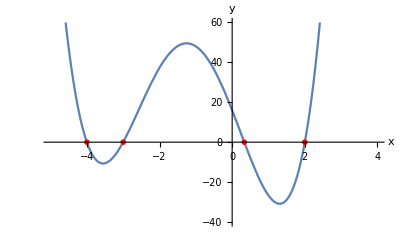

```mathematica
Plot[2x^4+(28/3)x^3-(22/3)x^2- (140/3)x + 16 , {x, -5,4}, PlotRange->{-40,60}, AxesLabel->{x,y}, Epilog->{Red, PointSize[0.01], Point[{-4, 0}], Point[{-3,0}], Point[{1/3,0}], Point[{2,0}]}]
```

## Olikhet

### Uppgift 21

```mathematica
Reduce[ {(x-2)/(x^2+1)>=0}, x, Reals]
```

x≥2

```mathematica
Reduce[{2/(3x-1)<=1}, x,Reals]
```

x<1/3||x≥1

```mathematica
Reduce[{4/(x^2+4)>=1/2}, x, Reals]
```

-2≤x≤2

```mathematica
Reduce[{(x-2)/(x^2-1)>=0},x,Reals]
```

-1<x<1||x≥2

```mathematica
Reduce[{(x-2)/(x-1)>=1+(2x)/(x+1)}, x,Reals]
```

-1<x<1

### Uppgift 22

```mathematica
Reduce[{Sqrt[x+1]<= - Sqrt[(2+x)]},x,Reals]
```

False

```mathematica
Reduce[{Sqrt[2x-1]>- Sqrt[(3-x)]},x,Reals]
```

1/2≤x≤3

```mathematica
Reduce[{Sqrt[x^2-1]>= Sqrt[2x^2-2x]},x,Reals]
```

x==1

```mathematica
Reduce[{2+Sqrt[x]>= x},x,Reals]
```

0≤x≤4

### Uppgift 26

```mathematica
Reduce[Abs[x-1]+Abs[x-2]==5,x,Reals]
```

x==-1||x==4

```mathematica
Reduce[Abs[x^2-x-2]==2,x,Reals]
```

x==0||x==1||x==1/2 (1-√17)||x==1/2 (1+√17)

## Binomisk ekvation

z^5=-3+3i

## Arean av en cirkel och närmevärde till Pi

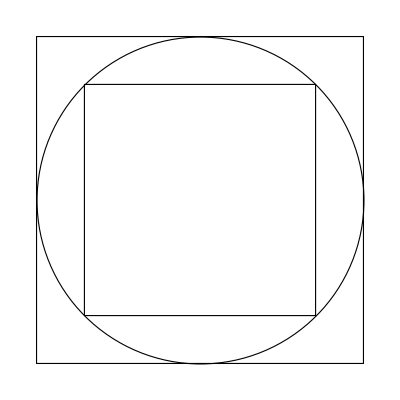

```mathematica
Show[Graphics[{FaceForm[None],EdgeForm[{Black}],Polygon[{{-1/Sqrt[2],-1/Sqrt[2]},{-1/Sqrt[2],1/Sqrt[2]},{1/Sqrt[2],1/Sqrt[2]} ,{1/Sqrt[2], -1/Sqrt[2]}}],Disk[{0, 0}],Polygon[{{-1, -1}, {-1, 1},{1, 1},{1, -1}}]}]]
```